```mathematica
yyy+1/x yy-2y=x^2;
x0=0.5;
yy0=-0.5;
y0=-1;
```

6

{0.5,0.6,0.7,0.8,0.9,1.}

{{},-1.05,-1.11145,-1.18102,-1.25874,-1.34457}

{{},-0.575,-0.655549,-0.73676,-0.817943,-0.89853}

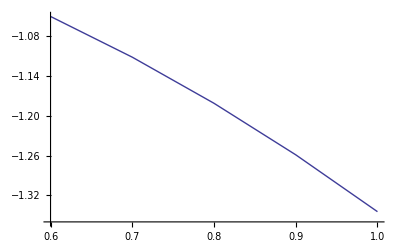

```mathematica
f1[x_,y_,z_]:=z;(*y'*)
f2[x_,y_,z_]:=x^2-1/x z + 2y; (*z'*)
y0=-1;
z0=-0.5;
a=0.5;
b=1;
h=0.1;
(*n=(b-a)/h+1;*)
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Z=Table[{},{n}];
Y2=Table[{},{n}];
Z2=Table[{},{n}];
Y2[[1]]=y0;
Z2[[1]]=z0;
For[i=2,i≤n,i++,
Y[[i]]=Y2[[i-1]]+h*f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Z[[i]]=Z2[[i-1]]+h*f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Y2[[i]]=Y2[[i-1]]+h*(f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f1[X[[i]],Y[[i]],Z[[i]]])/2;
Z2[[i]]=Z2[[i-1]]+h*(f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f2[X[[i]],Y2[[i]],Z[[i]]])/2;
];
Print[Y];
Print[Z];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y[[i]]};
]
ListLinePlot[dots]
```